# Daily death cases normalized to the total population

## Graph Generation Function

```mathematica
generateSupergraph[structure_,graphDistribution_,edgeThickness_:1]:=Module[{clusters,g,previousCount=0,vertices,edges,connectingEdges},clusters=Table[Module[{cluster},cluster=IndexGraph[RandomGraph[graphDistribution],previousCount];
previousCount+=VertexCount[cluster];
{VertexList[cluster],EdgeList[cluster]}],{i,VertexCount[structure]}];
{vertices,edges}=Union@@@Transpose[clusters];
connectingEdges=UndirectedEdge@@RandomChoice@*First/@clusters[[{#1,#2}]]&@@@Catenate[ConstantArray[EdgeList[structure],edgeThickness]];
Graph[vertices,Join[edges,connectingEdges]]]
```

## Simulate Function

```mathematica
simulate[neighbors_,meetingCounts_,recoveryTime_,initialInfected_List,maxSteps_,loggingFunc_]:=Module[{stateAgents,agentRecoveryTimes,agentMeetings,steps,output},agentMeetings[a_]:=RandomSample[neighbors[a],UpTo@Ramp@Round@RandomVariate[meetingCounts[a]]];
agentRecoveryTimes=AssociationMap[RandomVariate[recoveryTime]&,initialInfected];
stateAgents=<|"S"->CreateDataStructure["HashSet",Complement[Keys[neighbors],initialInfected]],"I"->CreateDataStructure["HashSet",initialInfected],"R"->CreateDataStructure["HashSet"]|>;
output={loggingFunc[stateAgents]};
steps=0;
While[steps++<maxSteps&&stateAgents["I"]["Length"]>0,Module[{newStateAgents},newStateAgents=#["Copy"]&/@stateAgents;
(*Mark appropriate agents as recovered*)KeyValueMap[If[#2<=0,KeyDropFrom[agentRecoveryTimes,#1];
newStateAgents["I"]["Remove",#1];
newStateAgents["R"]["Insert",#1];]&,agentRecoveryTimes];
(*Make infected agents meet their neighbors*)Function[infectedAgent,Module[{newInfected},newInfected=Select[agentMeetings[infectedAgent],stateAgents["S"]["MemberQ",#]&];
newStateAgents["S"]["Remove",#]&/@newInfected;
newStateAgents["I"]["Union",newInfected];
(agentRecoveryTimes[#]=RandomVariate[recoveryTime])&/@newInfected;]]/@Normal[stateAgents["I"]];
(*Make the susceptible neighbors of infected agents meet their neighbors*)Function[neighborOfInfected,Module[{metInfected},If[stateAgents["S"]["MemberQ",neighborOfInfected],metInfected=AnyTrue[agentMeetings[neighborOfInfected],stateAgents["I"]["MemberQ",#]&];
If[metInfected,newStateAgents["S"]["Remove",neighborOfInfected];
newStateAgents["I"]["Insert",neighborOfInfected];
agentRecoveryTimes[neighborOfInfected]=RandomVariate[recoveryTime];]]]]/@Flatten[Lookup[neighbors,Normal[stateAgents["I"]]],1];
(*Decrement the recovery times*)agentRecoveryTimes-=1;
stateAgents=newStateAgents;];
AppendTo[output,loggingFunc[stateAgents]];];
output]

simulate[neighbors_,meetingCounts_,recoveryTime_,initialInfectedCount_Integer,maxSteps_,loggingFunc_]:=simulate[neighbors,meetingCounts,recoveryTime,RandomSample[Keys[neighbors],initialInfectedCount],maxSteps,loggingFunc]

simulate[neighbors_,meetingCounts_,recoveryTime_,initialInfectedSpec_,maxSteps_]:=simulate[neighbors,meetingCounts,recoveryTime,initialInfectedSpec,maxSteps,Function[stateAgents,#["Length"]&/@Lookup[stateAgents,{"I","S","R"}]]]
```

## Neighborhoods and Meeting Counts Assignment

```mathematica
agentNeighborhoods[g_] := Merge[Catenate[{#1->#2,#2->#1}&@@@EdgeList[g]],Identity];
```

```mathematica
Trend[simulation_,opts___]:=StackedListPlot[Transpose[simulation],Frame->{{True,False},{True,False}},FrameLabel->{"step","agents"},opts]
```

```mathematica
Graph1=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0, 3],5];
```

```mathematica
simulation1=Association@Table[k->simulate[agentNeighborhoods[Graph1],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[Graph1]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
ListAnimate[KeyValueMap[Trend[#2,PlotLabel->#1]&,simulation1],AnimationRunning->False]
```

```mathematica
Graph2=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.5, 3],5];
```

```mathematica
simulation2=Association@Table[k->simulate[agentNeighborhoods[Graph2],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[Graph2]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
ListAnimate[KeyValueMap[Trend[#2,PlotLabel->#1]&,simulation2],AnimationRunning->False]
```

```mathematica
Graph3=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,1, 5],5];
```

```mathematica
simulation3=Association@Table[k->simulate[agentNeighborhoods[Graph3],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[Graph3]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
ListAnimate[KeyValueMap[Trend[#2,PlotLabel->#1]&,simulation3],AnimationRunning->False]
```

```mathematica
data1 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_02_Septiembre_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data1],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data2 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_13_Enero_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data2],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data3 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_13_Febrero_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data3],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data4 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_16_Febrero_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data4],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data5 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_19_Junio_2020.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data5],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data6 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_19_Octubre_2020.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data6],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data7 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_21_Enero_2022.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data7],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data8 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_April_01_2020.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data8],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data9 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_April_07_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data9],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data10 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_August_10_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data10],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data11 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_January_17_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data11],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
data12 = Import["/home/felipe/Desktop/Thesis/Physics_analysis_Covid-19/Deaths_Cases_Database_Per_Day/Deaths_May_14_2021.xlsx"];
```

```mathematica
FindDistributionParameters[Flatten[data12],SinghMaddalaDistribution[q,a, b]];
```

```mathematica
Plot3D[Skewness[SinghMaddalaDistribution[k,a,20]],{a,0.6,0.8},{k,1,50},MeshFunctions->{#3&},MeshShading->ColorData[35,"ColorList"],AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
G1=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0, 5],5];
```

```mathematica
G2=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.1, 5],5];
```

```mathematica
G3=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.2, 5],5];
```

```mathematica
G4=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.3, 5],5];
```

```mathematica
G5=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.4, 5],5];
```

```mathematica
G6=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.5, 5],5];
```

```mathematica
G7=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.6, 5],5];
```

```mathematica
G8=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.7, 5],5];
```

```mathematica
G9=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.8, 5],5];
```

```mathematica
G10=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,0.9, 5],5];
```

```mathematica
G11=generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],217],WattsStrogatzGraphDistribution[100,1, 5],5];
```

```mathematica
S1=Association@Table[k->simulate[agentNeighborhoods[G1],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G1]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S2=Association@Table[k->simulate[agentNeighborhoods[G2],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G2]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S3=Association@Table[k->simulate[agentNeighborhoods[G3],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G3]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S4=Association@Table[k->simulate[agentNeighborhoods[G4],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G4]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S5=Association@Table[k->simulate[agentNeighborhoods[G5],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G5]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S6=Association@Table[k->simulate[agentNeighborhoods[G6],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G6]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S7=Association@Table[k->simulate[agentNeighborhoods[G7],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G7]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S8=Association@Table[k->simulate[agentNeighborhoods[G8],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G8]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S9=Association@
Table[k->simulate[agentNeighborhoods[G9],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G9]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S10=Association@Table[k->simulate[agentNeighborhoods[G10],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G10]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
S11=Association@Table[k->simulate[agentNeighborhoods[G11],AssociationMap[SinghMaddalaDistribution[k,0.6,0.4]&,VertexList[G11]],ExponentialDistribution[1/14],1,Infinity],{k,1,5,0.1}];
```

```mathematica
peakInfected[sim_]:=Max[sim[[All,1]]]/Total[sim[[1]]]
```

```mathematica
totalInfected[sim_]:=(sim[[-1,1]]+sim[[-1,3]])/Total[sim[[-1]]]
```

```mathematica
ListLinePlot3D[{KeyValueMap[List,peakInfected/@S1], KeyValueMap[List,peakInfected/@S2], KeyValueMap[List,peakInfected/@S3], KeyValueMap[List,peakInfected/@S4], KeyValueMap[List,peakInfected/@S5], KeyValueMap[List,peakInfected/@S6], KeyValueMap[List,peakInfected/@S7], KeyValueMap[List,peakInfected/@S8], KeyValueMap[List,peakInfected/@S9], KeyValueMap[List,peakInfected/@S10], KeyValueMap[List,peakInfected/@S11]},PlotTheme->"Detailed",PlotLegends->{{Simulation1,Simulation2,Simulation3,Simulation4,Simulation5,Simulation6,Simulation7,Simulation8,Simulation9,Simulation10}}]
```

-Graphics3D-

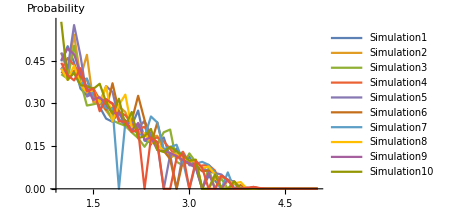

```mathematica
ListLinePlot[{KeyValueMap[List,peakInfected/@S1], KeyValueMap[List,peakInfected/@S2], KeyValueMap[List,peakInfected/@S3], KeyValueMap[List,peakInfected/@S4], KeyValueMap[List,peakInfected/@S5], KeyValueMap[List,peakInfected/@S6], KeyValueMap[List,peakInfected/@S7], KeyValueMap[List,peakInfected/@S8], KeyValueMap[List,peakInfected/@S9], KeyValueMap[List,peakInfected/@S10], KeyValueMap[List,peakInfected/@S11]},FillingStyle->Automatic, PlotLegends->{{Simulation1,Simulation2,Simulation3,Simulation4,Simulation5,Simulation6,Simulation7,Simulation8,Simulation9,Simulation10}},AxesLabel->Probability]
```